```mathematica
(* Analaytical solution for the enthalpy depth profile in Kleiner et al., 2015 Exp. b. *)
(* Equation numberts and pages refer to the book Greve& Blatter 2009 doi: 10.1007/978-3-642-03415-2 *)

ClearAll["Global`*"]
Clear[Derivative];
Remove["Global`*"];
(* a litle helper to preserve subscript m in Subscript[ζ, m] even though m is used elsewhere *) 
DynamicSymbolize[f_,k_]:=Symbolize[NotationBoxTag[SubscriptBox[f,k]]];
DynamicSymbolize["ζ","m"];
```

```mathematica
(* Eq 9.172, p. 249 *)
a5:=-k/(5*m);
a4:=k/m + d*k/m^2;
a3:=-2*k/m -4*d*k/m^2 -4 *d^2*k / m^3;
a2:=2*k/m+ 6*d*k/m^2 +12* d^2*k/m^3 + 12*d^3*k / m^4;
a1 := -k/m -4*d*k/m^2 - 12*d^2*k/m^3-24*d^3*k/m^4-24*d^4*k/m^5;
```

```mathematica
(* Eq: 9.173, p. 249 *)
Tc[zeta_]:=c1*Exp[-m/d*zeta] + c2 +a1*zeta+a2*zeta^2+a3*zeta^3+a4*zeta^4+a5*zeta^5;
(* Eq: 9.180, p250 *)
Wt[zeta_]:=kt/(5*m)((1-zeta)^5 - (1-zetam)^5);
(* D[Wt[zeta],zeta] *)
dWt[zeta_]:=-kt/m (1-zeta)^4;
Print["dW/dζ = ",D[Wt[zeta],zeta]]

(* horizontal velocity vx(zeta) Eq. 9.159 *)
vx[zeta_]:= A/2*(ρ*g*Sin[γ])^3 *(H^4 - (H-H*zeta)^4);
vx2[z_]:= A/2*(ρ*g*Sin[γ])^3 *(H^4 - (H-z)^4); (* z coordinates *)
(* temperature *)
T[zeta_]:= If[zeta>zetam,Tc[zeta],0];
(* water content *)
W[zeta_]:= If[zeta< zetam,Wt[zeta],0];
(* enthalpy *)
Enth[zeta_]:=Module[{E},
If[ zeta> zetam,E= c(T[zeta]+273.15-T0),E=Es + W[zeta]*L];
Return[E];
]
```

dW/dζ = -(kt (1-zeta)^4)/m

```mathematica
(* eff strainrate eff = 1/2(dvx/dz + dw/dx) = dvx/(H dzeta) *)
eff[zeta_]:=1/2*D[vx[zeta],zeta]/H;
eff2[z]:=1/2*D[vx2[z],z]; (* z coordinates *)
(* viscosity Eq. 4.20, p 56 *)
mu[zeta_] := 1/2 *A^(-1/3)*eff[zeta]^(-2/3);
mu2[z]:= 1/2 *A^(-1/3)*eff2[z]^(-2/3); (* z coordinates *)
(* strainheating *)
psi[zeta_] := 4 * mu[zeta] * eff[zeta]^2;
psi2[z]:=4 * mu2[z] * eff2[z]^2; (* z coordinates *)

(* debug printf's *)
Print["vx = ", vx2[z]]
Print["dvx/dz =", D[vx2[z],z]]
Print["eff = ",eff2[z]]
Print["mu = ", mu2[z]]
Print["psi = ", psi2[z]]
```

vx = 1/2 A g^3 (H^4-(H-z)^4) ρ^3 Sin[γ]^3

dvx/dz =2 A g^3 (H-z)^3 ρ^3 Sin[γ]^3

eff = A g^3 (H-z)^3 ρ^3 Sin[γ]^3

mu = 1/(2 A^(1/3) (A g^3 (H-z)^3 ρ^3 Sin[γ]^3)^(2/3))

psi = (2 A^(5/3) g^6 (H-z)^6 ρ^6 Sin[γ]^6)/((A g^3 (H-z)^3 ρ^3 Sin[γ]^3)^(2/3))

```mathematica
(* Eq 9.169, p 248 *)
d:= κ / (ρ*c);
m:= H *as;
k:= 2*A/(ρ*c)*H^6*(ρ*g*Sin[γ])^4;
kt:=2*A/(ρ*L)*H^6*(ρ*g*Sin[γ])^4;
Print["kt/m = ", kt/m]
```

kt/m = (2 A g^4 H^5 ρ^3 Sin[γ]^4)/(as L)

```mathematica
(* Fill in Values, see figure 9.24 on page 251 *)
spy = 31556926;
Ts=-3 ;
κ=2.1;
as = 0.2 / spy; 
H=200;
ρ = 910;
c=2009;
γ = 4 Degree;
g=9.81; 
A = 5.3 10^(-24); (* BENCHMARK*)
L = 3.35*10^5; (* 3.34 in Aschwanden et al 2012, 3.35 most other literature *)
T0 = 223.15; (* -50 degC reference temperature, better use -100 degC or belwo in an ice shelf model*)
Tpmp = 273.15; (* since beta is zero *)
Es= c*(Tpmp-T0);
```

```mathematica
(* the 3 equations for the unknowns c1, c2, Subscript[ζ, m] *)
eq9176:= Ts == c1 Exp[-m/d] + c2 +a1 +a2 +a3 +a4+a5;
eq9177:= 0 == c1 Exp[-m/d*zetam] + c2 +a1*zetam +a2*zetam^2 +a3*zetam^3 +a4*zetam^4+a5*zetam^5;
eq9178:= 0 == -m/d*c1 Exp[-m/d*zetam] +a1 +2*a2*zetam +3*a3*zetam^2 +4*a4*zetam^3+5*a5*zetam^4;
solc2=Solve[eq9177,c2];
solc1=Solve[eq9178,c1];
c1=c1/.solc1[[1]];
c2=c2/.solc2[[1]];
(* debug output *)
Print["c1 = ", c1]
Print["c2 = ", c2]
```

c1 = 0.906218 ⅇ^(1.10349 zetam) (-2136.29+2308.8 zetam-1176.71 zetam^2+335.669 zetam^3-44.0229 zetam^4)

c2 = -1. (-2136.29 zetam+1154.4 zetam^2-392.235 zetam^3+83.9173 zetam^4-8.80458 zetam^5+0.906218 (-2136.29+2308.8 zetam-1176.71 zetam^2+335.669 zetam^3-44.0229 zetam^4))

```mathematica
sol=NSolve[eq9176 && 0≤ zetam≤1,zetam];
zetam=zetam/.sol[[1]];
zm=H*zetam;
```

```mathematica
(* eff strainrate eff = 1/2(dvx/dz + dw/dx) = dvx/(H dzeta) *)
eff[zeta_]=0.5*D[vx[zeta],zeta]/H;
(* viscosity Eq. 4.20, p 56 *)
mu[zeta_] = 1/2 *A^(-1/3)*eff[zeta]^(-2/3);
(* strainheating *)
psi[zeta_] = 4 * mu[zeta] * eff[zeta]^2;
```

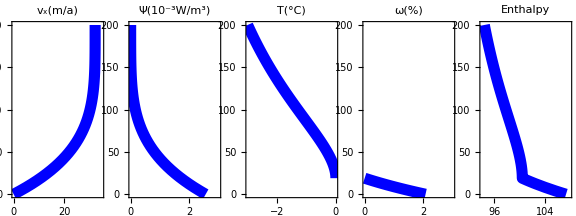

```mathematica
f1=ParametricPlot[{T[zeta],H*zeta},{zeta,zetam,1},Frame->True,AspectRatio->2/1,PlotRange->{{-3,0},{0,H}},PlotStyle->{{Thickness[0.02],Blue}},PlotLabel->"T(°C)"];
f2=ParametricPlot[{W[zeta]*100,H*zeta},{zeta,0,zetam},Frame->True,AspectRatio->2/1,PlotRange->{{0,3},{0,H}},PlotStyle->{{Thickness[0.02],Blue}},PlotLabel->"ω(%)"];
f3=ParametricPlot[{vx[zeta]*spy,H*zeta},{zeta,0,1},Frame->True,AspectRatio->2/1,PlotRange->{{0,35},{0,H}},PlotStyle->{{Thickness[0.02],Blue}},PlotLabel->"v_x(m/a)"];
f4=ParametricPlot[{psi[zeta]*10^3,H*zeta},{zeta,0,1},Frame->True,AspectRatio->2/1,PlotRange->{{0,3},{0,H}},PlotStyle->{{Thickness[0.02],Blue}},PlotLabel->"Ψ(10^-3W/m^3)"];
f5=ParametricPlot[{Enth[zeta]/1000,H*zeta},{zeta,0,1},Frame->True,AspectRatio->2/1,PlotRange->{{94,108},{0,H}},PlotStyle->{{Thickness[0.02],Blue}},PlotLabel->"Enthalpy"];


GraphicsRow[{f3,f4,f1,f2, f5},ImageSize->Large]
```

```mathematica
(* export figure *)
Export["profile_GreveBlatter.pdf",GraphicsRow[{f3,f4,f1,f2, f5},ImageSize->Large],"PDF"];
Export["profile_GreveBlatter_enthalpy.pdf",f5,"PDF"];
Export["profile_GreveBlatter_temperature.pdf",f1,"PDF"];
```

```mathematica
Print[ "A = ",A, "  ()"]
Print[ "ζ_m = ",zetam," and CTS = ",zm, " (m)"]
Print[ "T(ζ_m) = ",T[zetam]," (degC)"]
Print[ "W(ζ_m) = ",W[zetam]*100," (%)"]
Print[ "dW/dζ(ζ_m) = ",dWt[zetam]," ()"]
Print[ "W(ζ=0) = ",W[0]*100," (%)"]
Print[ "E(ζ=0) = ",Enth[0]/1000," (kJ/kg)"]
Print[ "Psi(ζ=0) = ",psi[0]*1000," (mW/m3)"]
Print[ "VX(ζ=1) = ",vx[1]*spy," (m/a)"]
```

A = 5.3×10^-24  ()

ζ_m = 0.0947342 and CTS = 18.9468 (m)

T(ζ_m) = 0 (degC)

W(ζ_m) = 0 (%)

dW/dζ(ζ_m) = -0.177304 ()

W(ζ=0) = 2.06998 (%)

E(ζ=0) = 107.384 (kJ/kg)

Psi(ζ=0) = 2.55038 (mW/m3)

VX(ζ=1) = 32.3106 (m/a)

## Export data

```mathematica
SetDirectory[NotebookDirectory[]]; (* set output directory *)
(* Directory[]*) (* check path *)
nz=401; (* -> DZ = 0.5 M *)
inc = 1 / (nz-1);
(* zeta layer *)
(*
dat=Table[{zeta//N,Enth[zeta]/1000,T[zeta],W[zeta]*100},{zeta,0,1,inc}];
filename=StringJoin["exp_b_analytic_nz_neu",IntegerString[nz,10,3],"_neu.dat"];
Export[filename,dat,"Table"];
*)

(* z layer *)
dat=Table[{zeta*H//N,Enth[zeta]/1000,T[zeta],W[zeta]*100},{zeta,0,1,inc}];
filename=StringJoin["exp_b_analytic_nz",IntegerString[nz,10,3],"_z.dat"];
Export[filename,dat,"Table"];
```

## DEBUG

```mathematica
(* zoom in to water content at cts *)
inc=1/100;
Table[{zeta//N,W[zeta],dWt[zeta]},{zeta,0,zetam,inc}]
zetam
W[zetam]
dWt[zetam]
```

{{0.,0.0206998,-0.264006},{0.01,0.018112,-0.253603},{0.02,0.0156267,-0.243511},{0.03,0.0132408,-0.233723},{0.04,0.0109512,-0.224233},{0.05,0.00875515,-0.215035},{0.06,0.0066496,-0.206123},{0.07,0.00463176,-0.19749},{0.08,0.00269888,-0.189132},{0.09,0.000848226,-0.181042}}

0.0947342

0

-0.177304

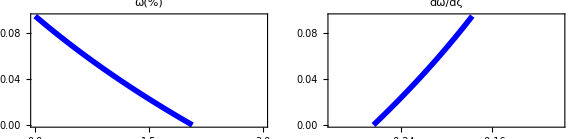

```mathematica
w1=ParametricPlot[{W[zeta]*100,zeta},{zeta,0,zetam},Frame->True,AspectRatio->1/2,PlotRange->{{0,3},{0,zetam}},PlotStyle->{{Thickness[0.01],Blue}},PlotLabel->"ω(%)"];
w2=ParametricPlot[{dWt[zeta],zeta},{zeta,0,zetam},Frame->True,AspectRatio->1/2,PlotRange->{{-0.3,-0.1},{0,zetam}},PlotStyle->{{Thickness[0.01],Blue}},PlotLabel->"dω/dζ"];
GraphicsRow[{w1,w2},ImageSize->Large]
```

```mathematica
Export["profile_GreveBlatter_omega.pdf",GraphicsRow[{w1,w2},ImageSize->Large],"PDF"];
```